```mathematica
(* https://github.com/shahin-mansouri *)
MyAdamBashforth[F_,h_,t_,y_][{t0_,y0_}]:=Module[{j,p,m,a,F0,F1,F2},m=8;
a=0;
t[0]=t0;
y[0]=y0;
For[j=0,j<=1,j++,t[j+1]=t[j]+h;
y[j+1]=y[j]+h*F[t[j],y[j]];];
F0=F[t[0],y[0]];
F1=F[t[1],y[1]];
F2=F[t[2],y[2]];
For[j=2,j<=m,j++,p=y[j]+h/12 (5 F0-16 F1+23 F2);
t[j+1]=t[j]+h;
y[j+1]=p;
F0=F1;
F1=F2;
F2=F[t[j+1],y[j+1]];];]
```

```mathematica
Clear[F,y,t,h];
F[t_,y_]:=t+y;
MyAdamBashforth[F,0.5,t,y][{0.,1.}]
MyData3=Table[{t[j],y[j]},{j,0,8}]

(*{{0.,1.},{0.5,1.5},{1.,2.5},{1.5,4.72917},{2.,8.78212},{2.5,15.6914},{3.,27.2344},{3.5,46.3278},{4.,77.713}}*)
```

{{0.,1.},{0.5,1.5},{1.,2.5},{1.5,4.72917},{2.,8.78212},{2.5,15.6914},{3.,27.2344},{3.5,46.3278},{4.,77.713}}

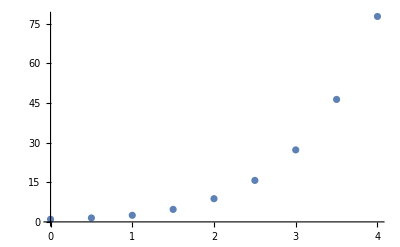

```mathematica
ListPlot[MyData3]
```